## Plotting the first incidence of C.auris sorted by time, country, and continent

```mathematica
data=Import[NotebookDirectory[]<>"auris-timeline.csv","CSV"];
```

```mathematica
cols=Short[ColorData[97,"ColorList"],4]⟦1⟧⟦1;;6⟧
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
data=Rest[data];
```

```mathematica
countries=data[[All,1]];
dates=data[[All,2]];
```

```mathematica
dateObjects=DateObject[{#}]&/@dates;
```

```mathematica
sorted=SortBy[Transpose[{dateObjects,countries}],First];
sortedDates=sorted[[All,1]];
sortedCountries=sorted[[All,2]];
```

```mathematica
continents=CountryData[#,"Continent"]&/@sortedCountries;
```

```mathematica
tallied=Tally[continents]⟦All,1⟧
```

{Europe,South America,North America,Asia,Africa,Oceania}

```mathematica
colorlist=continents/.{Table[tallied⟦i⟧->cols[[i]],{i,1,6}]};
```

```mathematica
topldata=sortedDates⟦4;;⟧;
```

```mathematica
splitrans=SplitBy[Transpose[{topldata,colorlist⟦1⟧⟦4;;⟧}],First];
```

```mathematica
contsorted=SortBy[#,Last]&/@splitrans;
```

```mathematica
colsort=Partition[Flatten[Table[SortBy[contsorted⟦i⟧,#⟦2⟧&],{i,1,Length[contsorted]}]],2]⟦All,2⟧;
```

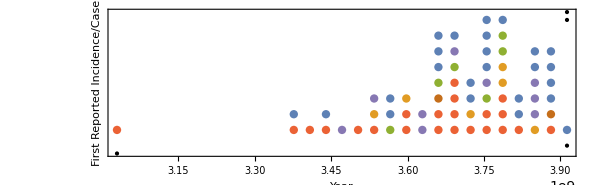

```mathematica
TimelinePlot[Style[topldata⟦#⟧,colsort⟦#⟧]&/@Range[1,69],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Year",Black,24],Style["First Reported\n Incidence/Case",Black,24]}]
```